# Math 152 Webpage Images

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
publish[picture_,name_]:=Module[{prefix},
prefix="_assets\\images\\";
Export[StringJoin[prefix,name,".png"],Show[picture,ImageSize->250]];
Export[StringJoin[prefix,name,".hd.png"],Show[picture,ImageSize->750]];
Show@picture
]
```

## Chapter 5

## Chapter 6

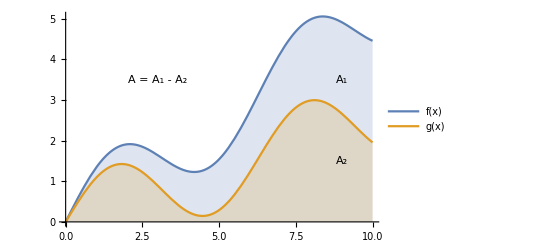

```mathematica
picture=Show[
Plot[{Sin[x]+x/2,Sin[x]+x/4},{x,0,10},PlotLegends->{f[x],g[x]},Filling->0],
Graphics@Style[Text["A_1",{9,3.5}],16],
Graphics@Style[Text["A_2",{9,1.5}],16],
Graphics@Style[Text["A = A_1 - A_2",{3,3.5}],16]
];
publish[picture,"6.1.01"]
```